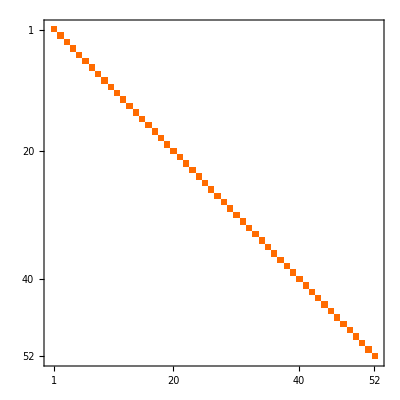
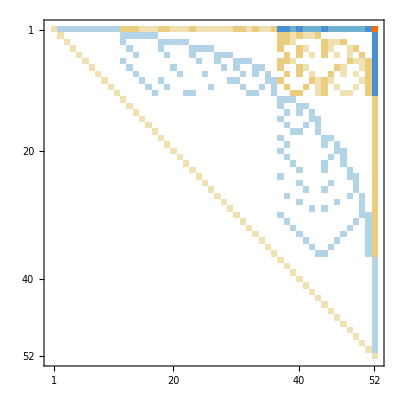
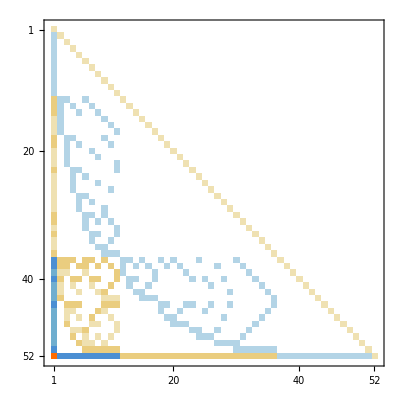
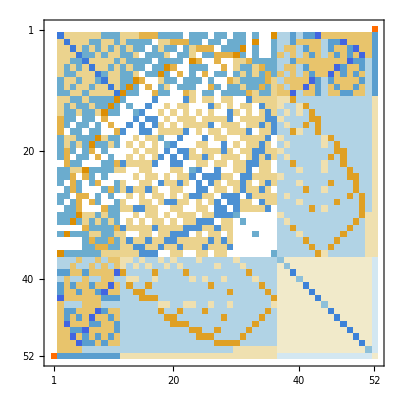
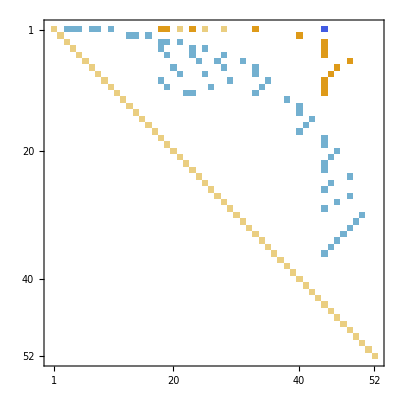
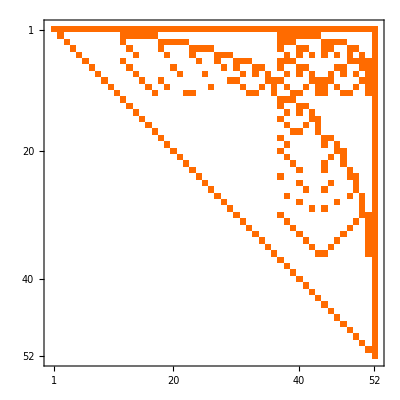
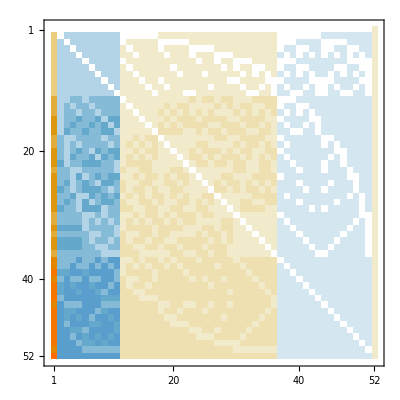
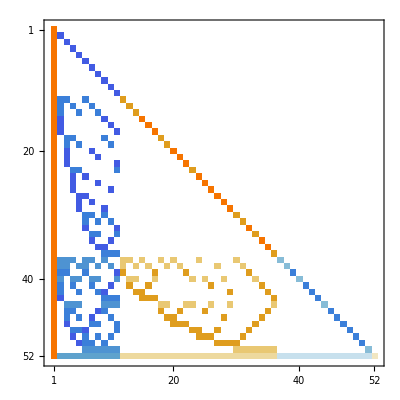
( | C | E | G | F | T
C | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
E | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
G | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
F | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
T | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-)

```mathematica
With[{bases=Keys[Bases]},
MatrixForm[Table[MatrixPlot[ConversionMatrix[base1,base2]],{base1,bases },{base2, bases}],TableHeadings->{bases, bases}]
]
```